Electron-positron pair production in the collision of real photon beams with wide energy distributions

L Esnault et al 2021 Plasma Phys. Control. Fusion 63 125015
Notebook: Óscar Amaro, October 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce Figures 3, 4 and 5

## Figure 3

1/s 3.28134 (-√(1-1.04448/s) (1+1.04448/s)+(2-1.09095/s^2+2.08897/s) Log[0.978474 (√(-1.04448+s)+√s)])

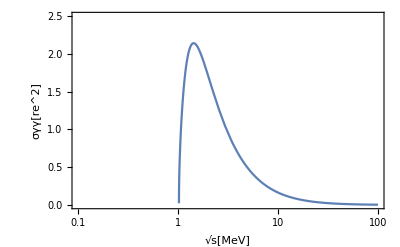

```mathematica
Clear[m,c,s,re,σγγ]
c=1;
m=0.511;
re=1;
σγγ=4π re^2 (m^2 c^4)/s((2+(8m^2c^4)/s-(16m^4c^8)/s^2)Log[(Sqrt[s]+Sqrt[s-4m^2c^4])/(2m c^2)]-Sqrt[1-(4m^2c^4)/s](1+(4m^2c^4)/s))
LogLinearPlot[σγγ/.{s->sqrts^2},{sqrts,10^-1,10^2},PlotRange->{{10^-1,10^2},{0,2.5}},Frame->True,FrameLabel->{"√s[MeV]","σγγ[re^2]"}]
```

```mathematica
(* peak of cross section occurs at s=2.06 MeV^2*)
FindMaximum[σγγ,{s,1.1}]
```

{2.14164,{s→2.05544}}

```mathematica
(* peak of cross section/10 occurs at s=71.7 MeV^2, as mentioned in caption of Figure 6*)
FindRoot[σγγ-2.1416410079961308/10,{s,2}]
```

{s→71.7428+2.49495×10^-19 ⅈ}

## Figure 4

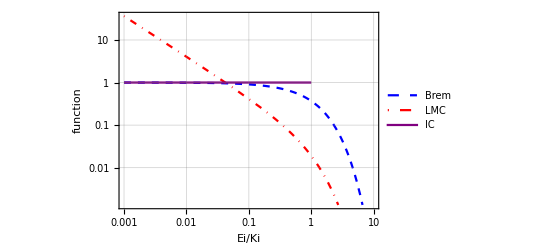

```mathematica
LogLogPlot[{Exp[-EiKi],1/Gamma[0.05](EiKi)^(-0.95)Exp[-EiKi],HeavisideTheta[1-EiKi]},{EiKi,10^-3,10^1},PlotLegends->{"Brem","LMC","IC"},Frame->True,FrameLabel->{"Ei/Ki","function"},PlotPoints->10,Filling->None,PlotStyle->{Directive[Blue,Dashed],Directive[Red,DotDashed],Directive[Purple]},GridLines->Automatic]
```

```mathematica
(* the "theoretical" distributions are already normalized *)
Clear[EiKi]
Integrate[Exp[-EiKi],{EiKi,0,∞}]
Integrate[1/Gamma[0.05](EiKi)^(-0.95)Exp[-EiKi],{EiKi,0,∞}]
Integrate[HeavisideTheta[1-EiKi],{EiKi,0,∞}]
```

1

1.

1

## Figure 5: numerical integrals and fitted functions

```mathematica
Clear[h,ζ,a,b,n,m,re]
Clear[m,c,s,re,σγγ,smin]
Clear[gBremBrem,gLMCLMC,gICIC,σ11BremBrem,σ11LMCLMC,σ11ICIC,intgBremBrem,intgLMCLMC,intgICIC,logsqrtζmin,dlogsqrtζ]
c=1;
m=0.511;
re=1;
σγγ[s_?NumericQ]:=σγγ[s]=4π re^2 (m^2 c^4)/s((2+(8m^2c^4)/s-(16m^4c^8)/s^2)Log[(Sqrt[s]+Sqrt[s-4m^2c^4])/(2m c^2)]-Sqrt[1-(4m^2c^4)/s](1+(4m^2c^4)/s))

(* we can only integrate for s>4m^2c^4 *)
smin=4m^2c^4;

gBremBrem[EiKi_?NumericQ]:=gBremBrem[EiKi]=Exp[-EiKi]//Quiet
gLMCLMC[EiKi_?NumericQ]:=gLMCLMC[EiKi]=1/Gamma[0.05](EiKi)^(-0.95)Exp[-EiKi]//Quiet
gICIC[EiKi_?NumericQ]:=gICIC[EiKi]=HeavisideTheta[1-EiKi]//Quiet

intgBremBrem[η_?NumericQ]:=intgBremBrem[η]=NIntegrate[gBremBrem[s/η]σγγ[s],{s,smin,∞}]//Quiet
σ11BremBrem[ζ_]:=1/ζ NIntegrate[gBremBrem[η/ζ]/η intgBremBrem[η],{η,0,∞}]//Quiet

intgLMCLMC[η_?NumericQ]:=intgLMCLMC[η]=NIntegrate[gLMCLMC[s/η]σγγ[s],{s,smin,∞}]//Quiet
σ11LMCLMC[ζ_]:=1/ζ NIntegrate[gLMCLMC[η/ζ]/η intgLMCLMC[η],{η,0,∞}]//Quiet

intgICIC[η_?NumericQ]:=intgICIC[η]=NIntegrate[gICIC[s/η]σγγ[s],{s,smin,∞}]//Quiet
σ11ICIC[ζ_]:=1/ζ NIntegrate[gICIC[η/ζ]/η intgICIC[η],{η,0,∞}]//Quiet

(* generate data for figure 5 *)
(* logsqrtζ=Log10[Sqrt[ζ]] -> ζ=(10^logsqrtζ)^2*)
logsqrtζmin=-0.9;
dlogsqrtζ=0.03;
lstσ11BremBrem=ParallelTable[{(10^logsqrtζ),σ11BremBrem[(10^logsqrtζ)^2]},{logsqrtζ,logsqrtζmin,5,dlogsqrtζ}];
lstσ11LMCLMC=ParallelTable[{(10^logsqrtζ),σ11LMCLMC[(10^logsqrtζ)^2]},{logsqrtζ,logsqrtζmin,5,dlogsqrtζ}];
lstσ11ICIC=ParallelTable[{(10^logsqrtζ),σ11ICIC[(10^logsqrtζ)^2]},{logsqrtζ,logsqrtζmin,5,dlogsqrtζ}];
```

Plot generated data and fits (from parameters in paper, not from the data generated here)

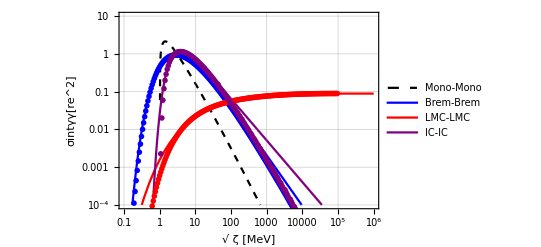

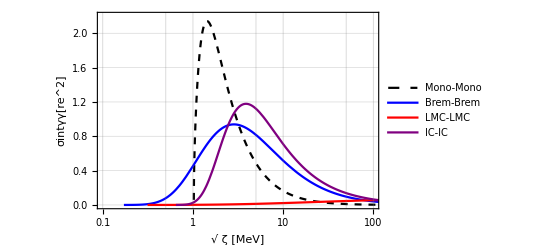

```mathematica
Clear[h,ζ,a,b,n,m,re]
Clear[m,c,s,re,σγγ]
c=1;
m=0.511;
re=1;
σγγ=4π re^2 (m^2 c^4)/s((2+(8m^2c^4)/s-(16m^4c^8)/s^2)Log[(Sqrt[s]+Sqrt[s-4m^2c^4])/(2m c^2)]-Sqrt[1-(4m^2c^4)/s](1+(4m^2c^4)/s));
h[ζ_,a_,b_,n_,m_]:=re^2 (a/ζ^n)Exp[-b/ζ^m]
Show[{LogLogPlot[{σγγ/.{s->sqrtζ^2},h[sqrtζ^2,23.3,3.94,0.674,0.374],h[sqrtζ^2,9.82 10^-2,4.13,3.32 10^-3,0.221],h[sqrtζ^2,10.5,6.01,0.552,0.798]},{sqrtζ,10^-1,10^6},PlotStyle->{Directive[Black,Dashed],Directive[Blue],Directive[Red],Directive[Purple]},PlotRange->{{10^-1,10^6},{10^-4,10^1}},PlotLegends->{"Mono-Mono","Brem-Brem","LMC-LMC","IC-IC"},GridLines->Automatic,Frame->True,FrameLabel->{"√ ζ [MeV]","σintγγ[re^2]"}],ListLogLogPlot[{lstσ11BremBrem,lstσ11LMCLMC,lstσ11ICIC},PlotStyle->{Directive[Blue,PointSize[0.01]],Directive[Red,PointSize[0.01]],Directive[Purple,PointSize[0.01]]},PlotRange->{{10^-1,10^6},{10^-4,10^1}}]}]
LogLinearPlot[{σγγ/.{s->sqrtζ^2},h[sqrtζ^2,23.3,3.94,0.674,0.374],h[sqrtζ^2,9.82 10^-2,4.13,3.32 10^-3,0.221],h[sqrtζ^2,10.5,6.01,0.552,0.798]},{sqrtζ,10^-1,10^6},PlotStyle->{Directive[Black,Dashed],Directive[Blue],Directive[Red],Directive[Purple]},PlotRange->{{10^-1,10^2},{10^-4,2.2}},PlotLegends->{"Mono-Mono","Brem-Brem","LMC-LMC","IC-IC"},GridLines->Automatic,Frame->True,FrameLabel->{"√ ζ [MeV]","σintγγ[re^2]"}]
```